## Ventana Gaussiana

Ecuación correspondiente al ancho de la ventana de las curvas gaussianas para la estimación de los parámetros de la matriz de transformación.

```mathematica
Clear[a,b]
Rec[x_]=a x^2+b;(*Función parabólica*)
p1=0.2;(*Punto inferior para x=5000*)
p2 = 2;(*Punto inferior para x=1*)
```

```mathematica
pars=Solve[Rec[1]-p2==0&&Rec[5000]-p1==0,{a,b}];
```

```mathematica
{a}=pars[[All,1,2]]
{b}=pars[[All,2,2]]
```

{-7.2×10^-8}

{2.}

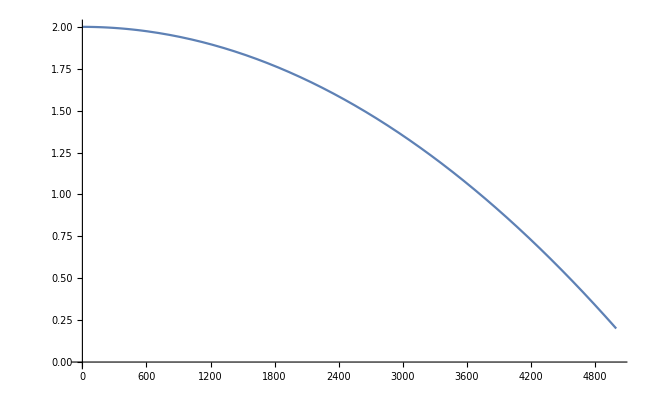

```mathematica
f[x_]=(a)(x^2) + b;
Plot[f[x],{x,1,5000}]
```